```mathematica
(* Create global definitions and set up workspace for all subsequent work *)
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
SetDirectory["./Solutions"];
<<setup_workspace.m;
<<setup_definitions.m;
```

Exporting:discreteApprox

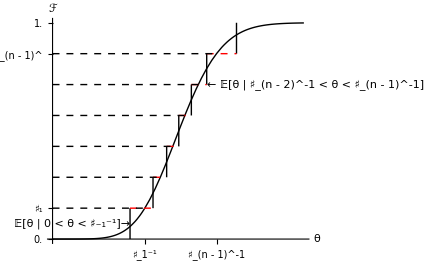

```mathematica
(* Read in baseline parameters and construct baseline shocks then make discreteApprox figure *)
<<setup_params.m;
<<setup_shocks.m;
<<discreteApprox!Plot.m;
```

```mathematica
(* Set up for solution of 2 period model and construction of figures *)
<<setup_params_2period.m;
<<setup_grids.m;
<<setup_shocks.m;
<<setup_lastperiod.m;
<<setup_PerfectForesightSolution.m;
```

Solve 2period model using brute force (no tricks or approximations) and plot.

Exporting:vTm1Plot

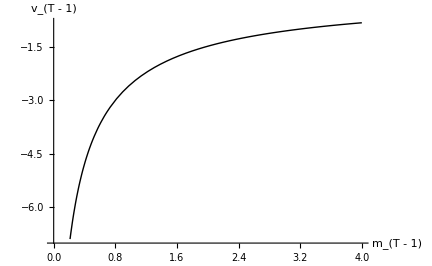

Exporting:cTm1Plot

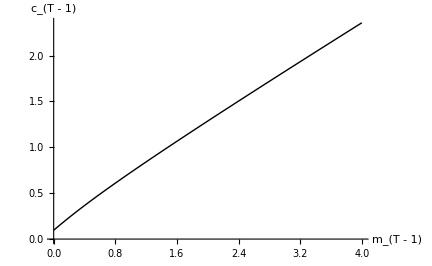

```mathematica
<<2Period!Plot.m;
```

Solve 2period model using linear interpolation.

Exporting:PlotVTm1Simple

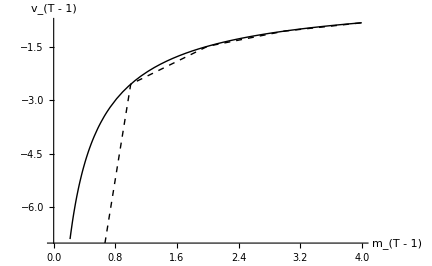

Exporting:PlotcTm1Simple

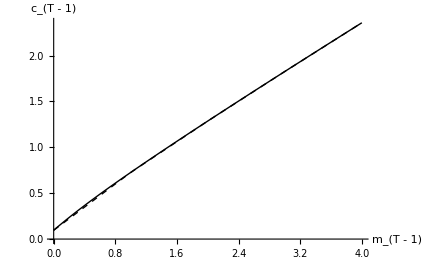

```mathematica
<<2PeriodInt!Plot.m;
```

InterpolatingFunction::dmval: Input value {-0.0663635} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindMaximum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.827347, 0.143261, 0.413675}, is returned.

FindMaximum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.0223013, 0.0134804, 0.0111506}, is returned.

Solve 2period model by interpolating expectations.

Exporting:PlotOTm1RawVSInt

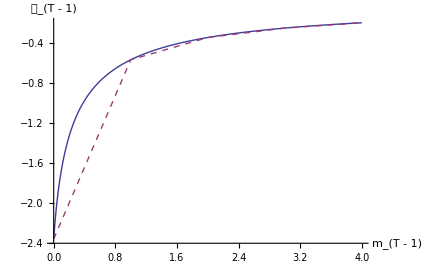

Exporting:PlotCompareVTm1AB

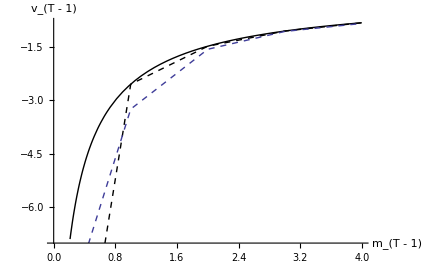

Exporting:PlotComparecTm1AB

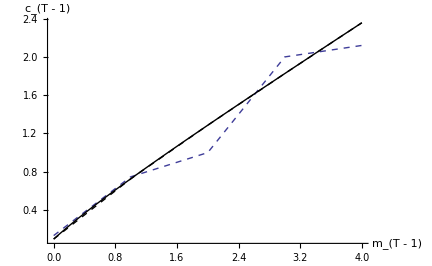

Exporting:PlotuPrimeVSOPrime

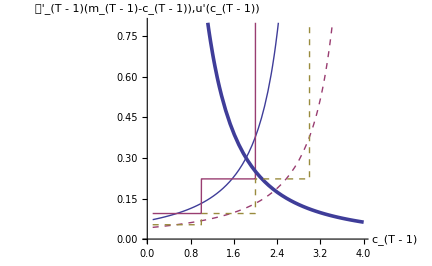

```mathematica
<<2periodIntExp!Plot.m;
```

InterpolatingFunction::dmval: Input value {-0.0663635} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Solve using the FOC, rather than the level of value.

Exporting:PlotGothVRawVSFOC

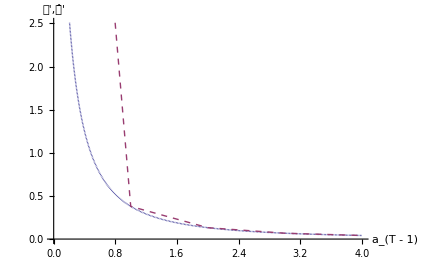

Exporting:PlotcTm1ABC

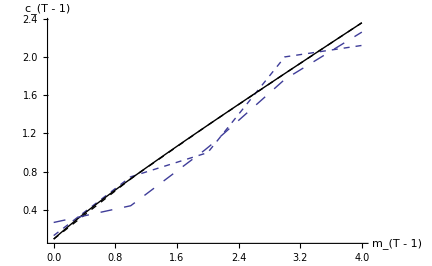

```mathematica
<<2periodIntExpFOC!Plot.m;
```

Solve using the inverse (transformed) versions of the functions.

Exporting:GothVInvVSGothC

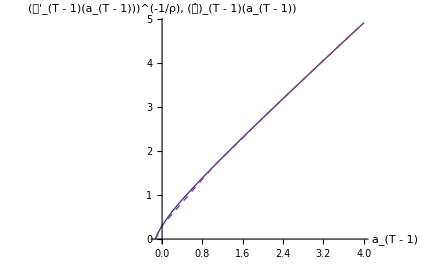

Exporting:GothVVSGothCInv

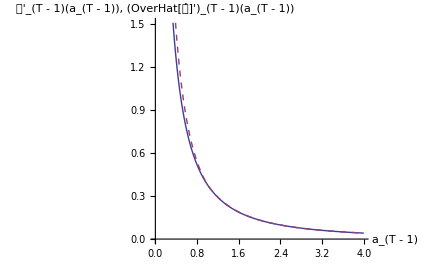

Exporting:PlotComparecTm1AD

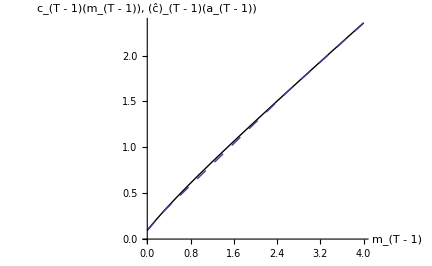

```mathematica
<<2periodIntExpFOCInv!Plot.m;
```

Use a triple-exponential to construct aVec.

Exporting:GothVInvVSGothCEEE

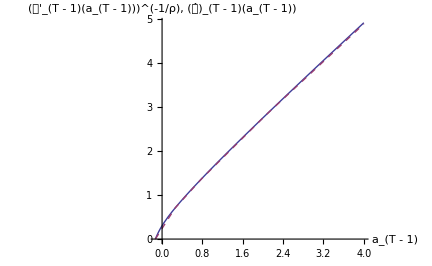

Exporting:GothVVSGothCInvEEE

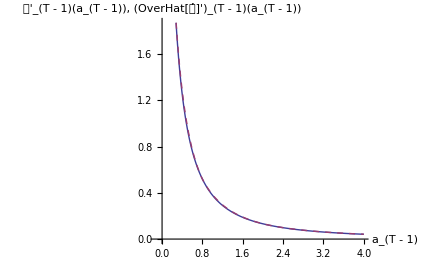

Exporting:PlotComparecTm1ADEEE

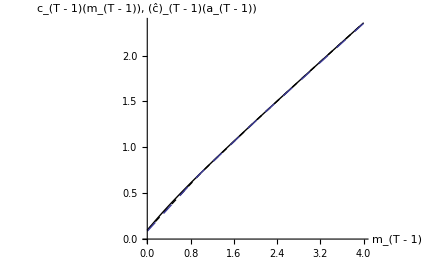

```mathematica
<<2periodIntExpFOCInvEEE!Plot.m;
```

Exporting:ExtrapProblemPlot

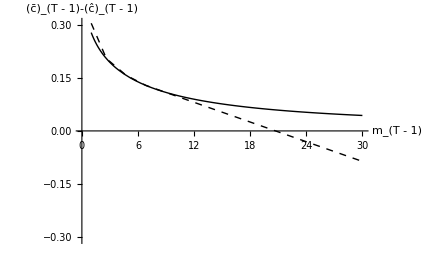

```mathematica
<<ExtrapProblem!Plot.m;
```

Exporting:ExtrapProblemSolvedPlot

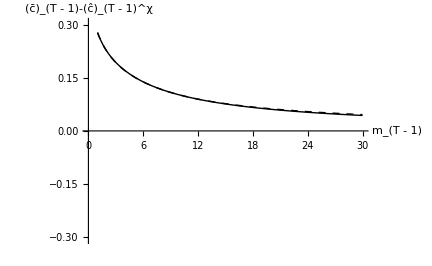

```mathematica
<<ExtrapProblemSolved!Plot.m;
```

Use the 'method of moderation.'

Exporting:IntExpFOCInvPesReaOptGapPlot

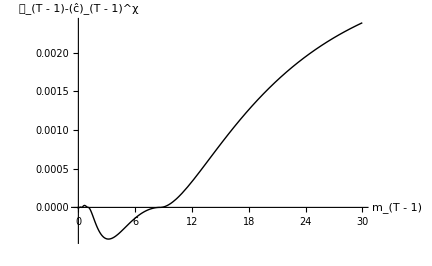

```mathematica
<<2PeriodIntExpFOCInvPesReaOpt!Plot.m;
```

Use the 'method of moderation' to solve constrained model.'

Exporting:cVScCon

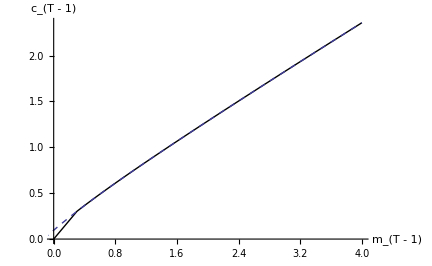

```mathematica
<<2PeriodIntExpFOCInvPesReaOptCon!Plot.m;
```

Exporting:PlotCFuncsConverge

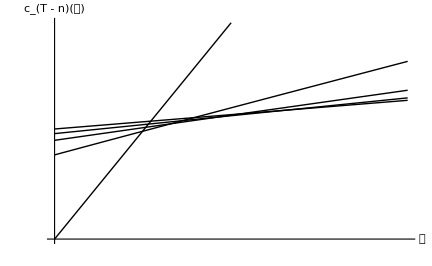

```mathematica
<<multiperiod!Plot.m;
```

Exporting:PlotCFuncsConverge

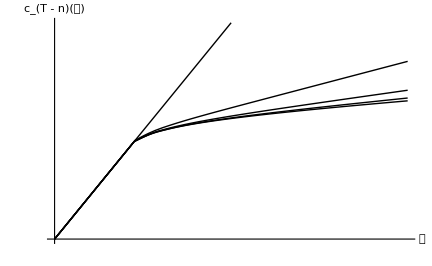

```mathematica
<<multiperiodCon!Plot.m;
```

InterpolatingFunction::dmval: Input value {133.949} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {134.067} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {134.142} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Exporting:PlotctMultContr

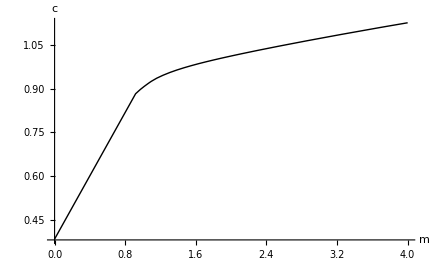

Exporting:PlotRiskySharetOfat

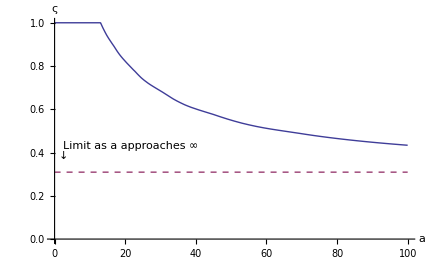

```mathematica
<<multicontrol!Plot.m;
```